```mathematica
obj=ResourceObject["CIFAR-100"];
```

```mathematica
trainingData=ResourceData[obj,"TrainingData"];
```

```mathematica
RandomSample[trainingData, 5]
```

{-Graphics-→poppy,-Graphics-→poppy,-Graphics-→pear,-Graphics-→fox,-Graphics-→can}

```mathematica
convnet=NetChain[{ConvolutionLayer[20,{5,5}],ElementwiseLayer[Ramp],PoolingLayer[{2,2},{2,2}],ConvolutionLayer[50,{5,5}],ElementwiseLayer[Ramp],PoolingLayer[{2,2},{2,2}],FlattenLayer[],DotPlusLayer[500],ElementwiseLayer[Ramp]},"Input"->NetEncoder[{"Image",{32,32}}]]
```

NetChain[]

```mathematica
net = NetTrain[convnet, trainingData]
```

NetTrain::invindim: Data provided to port "Output" should be a list of length-500 vectors.

$Failed

```mathematica
classes=Union@Values[trainingData]
```

{apple,aquarium fish,baby,bear,beaver,bed,bee,beetle,bicycle,bottle,bowl,boy,bridge,bus,butterfly,camel,can,castle,caterpillar,cattle,chair,chimpanzee,clock,cloud,cockroach,computer keyboard,couch,crab,crocodile,cup,dinosaur,dolphin,elephant,flatfish,forest,fox,girl,hamster,house,kangaroo,lamp,lawn-mower,leopard,lion,lizard,lobster,man,maple tree,motorcycle,mountain,mouse,mushroom,oak tree,orange,orchid,otter,palm tree,pear,pickup truck,pine tree,plain,plate,poppy,porcupine,possum,rabbit,raccoon,ray,road,rocket,rose,sea,seal,shark,shrew,skunk,skyscraper,snail,snake,spider,squirrel,streetcar,sunflower,sweet pepper,table,tank,telephone,television,tiger,tractor,train,trout,tulip,turtle,wardrobe,whale,willow tree,wolf,woman,worm}

```mathematica
lenet=NetChain[{ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],FlattenLayer[],500,Ramp,100,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",classes}],"Input"->NetEncoder[{"Image",{32,32}}]]
```

NetChain[]

```mathematica
trained=NetTrain[lenet,trainingData,MaxTrainingRounds->4]
```

NetChain[]

```mathematica
trained[{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

{pickup truck,maple tree,beaver,spider,motorcycle}

```mathematica
trained[-Graphics-, {"TopProbabilities", 3}]
```

{cattle→0.0918845,kangaroo→0.0719318,rabbit→0.0617032}

```mathematica
images=RandomSample[Keys[trainingData],5000];
```

```mathematica
entropies=trained[images,"Entropy"];
```

```mathematica
Labeled[images[[Ordering[entropies,-10]]],"high entropy"] Labeled[images[[Ordering[entropies,10]]],"low entropy"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}high entropy {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}low entropy

```mathematica
trained[{-Graphics-}]
```

{sunflower}

```mathematica
trained=NetTrain[lenet,trainingData,MaxTrainingRounds->8]
```

NetChain[]

```mathematica
trained[{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

{pickup truck,tiger,mountain,lizard,tulip}

```mathematica
trained[-Graphics-, {"TopProbabilities", 3}]
```

{raccoon→0.10679,porcupine→0.0909748,crocodile→0.0903858}

```mathematica
images=RandomSample[Keys[trainingData],5000];
```

```mathematica
entropies=trained[images,"Entropy"];
```

```mathematica
Labeled[images[[Ordering[entropies,-10]]],"high entropy"] Labeled[images[[Ordering[entropies,10]]],"low entropy"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}high entropy {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}low entropy

```mathematica
trained[{-Graphics-}]
```

{lawn-mower}

```mathematica
trained[{-Graphics-}]
```

{chair}

```mathematica
testData=ResourceData[obj,"TestData"];
```

```mathematica
trainingData=ResourceData[obj,"TestData"];
```

```mathematica
entropies=trained[images,"Entropy"];
```

```mathematica
Labeled[images[[Ordering[entropies,-10]]],"high entropy"] Labeled[images[[Ordering[entropies,10]]],"low entropy"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}high entropy {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}low entropy

```mathematica
images=RandomSample[Keys[trainingData],5000];
```

```mathematica
images=RandomSample[Keys[testData],5000];
```

```mathematica
entropies=trained[images,"Entropy"];
```

```mathematica
Labeled[images[[Ordering[entropies,-10]]],"high entropy"] Labeled[images[[Ordering[entropies,10]]],"low entropy"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}high entropy {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}low entropy

```mathematica
trained[{-Graphics-}]
```

{fox}

```mathematica
trained[{-Graphics-}]
```

{bicycle}

```mathematica
trained[{-Graphics-}]
```

{lawn-mower}

```mathematica
testData
```

{-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,9928,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm}
 |  |  |  |

```mathematica
trained[{-Graphics-}]
```

{pear}

```mathematica
trained[{-Graphics-}]
```

{apple}

```mathematica
trained[{-Graphics-}]
```

{worm}

```mathematica
trained[{-Graphics-}]
```

{lion}

```mathematica
c = Classify[trained]
```

ClassifierFunction[…]

```mathematica
cm = ClassifierMeasurements[c, testData]
```

ClassifierMeasurementsObject[…]

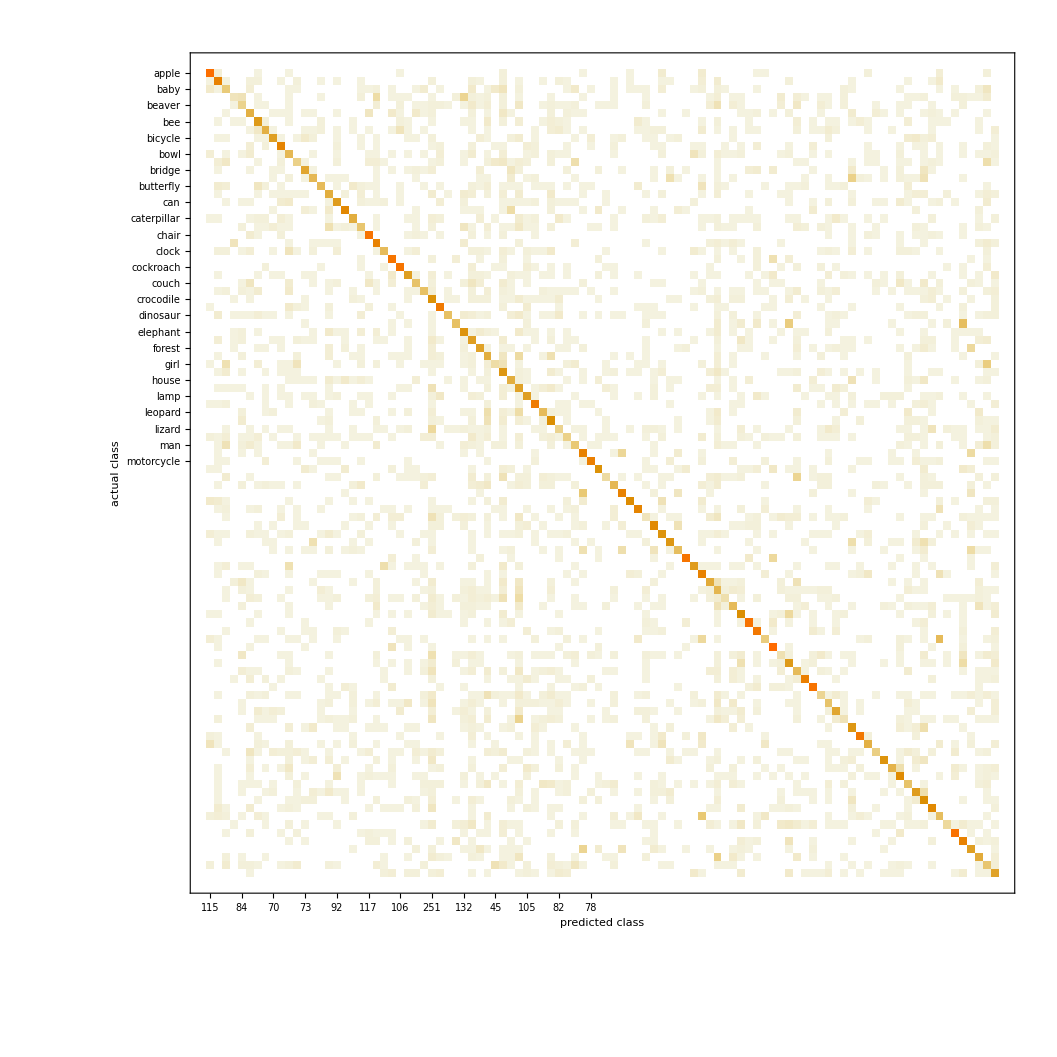
0.3802
<|apple→0.67907,aquarium fish→0.495495,baby→0.214286,bear→0.125,beaver→0.184783,bed→0.28972,bee→0.386792,beetle→0.358382,bicycle→0.458824,bottle→0.532663,bowl→0.25,boy→0.214286,bridge→0.416185,bus→0.318182,butterfly→0.350649,camel→0.301887,can→0.416667,castle→0.552486,caterpillar→0.374269,cattle→0.267442,chair→0.635945,chimpanzee→0.458333,clock→0.348387,cloud→0.578723,cockroach→0.660194,computer keyboard→0.423913,couch→0.280702,crab→0.30303,crocodile→0.250712,cup→0.586047,dinosaur→0.37037,dolphin→0.33557,elephant→0.37069,flatfish→0.27758,forest→0.374384,fox→0.238806,girl→0.165517,hamster→0.268371,house→0.321608,kangaroo→0.222874,lamp→0.380488,lawn-mower→0.587678,leopard→0.319527,lion→0.354331,lizard→0.186813,lobster→0.211765,man→0.236559,maple tree→0.458333,motorcycle→0.651685,mountain→0.488889,mouse→0.192593,mushroom→0.312849,oak tree→0.552764,orange→0.562874,orchid→0.552083,otter→0.100629,palm tree→0.478049,pear→0.407583,pickup truck→0.461538,pine tree→0.313253,plain→0.735135,plate→0.465116,poppy→0.423077,porcupine→0.364641,possum→0.17737,rabbit→0.164179,raccoon→0.274112,ray→0.382979,road→0.686567,rocket→0.551724,rose→0.261438,sea→0.644068,seal→0.130719,shark→0.348936,shrew→0.229787,skunk→0.644444,skyscraper→0.64486,snail→0.201258,snake→0.243655,spider→0.382979,squirrel→0.122449,streetcar→0.355932,sunflower→0.684492,sweet pepper→0.366864,table→0.269504,tank→0.534161,telephone→0.405405,television→0.426667,tiger→0.248705,tractor→0.39604,train→0.320285,trout→0.457944,tulip→0.247619,turtle→0.215385,wardrobe→0.7,whale→0.438247,willow tree→0.361111,wolf→0.320388,woman→0.18254,worm→0.308943|>
-Graphics-

```mathematica
cm/@{"Accuracy","FScore","ConfusionMatrixPlot"}//TableForm
```

```mathematica
ClassifierMeasurements[c,testData,"Accuracy"]
```

0.3802

```mathematica
ClassifierMeasurements[c,testset,"Precision"]
```

ClassifierMeasurements::bdfmt: Argument testset should be a rule, a list of rules, or an association.

ClassifierMeasurements[ClassifierFunction[…],testset,Precision]

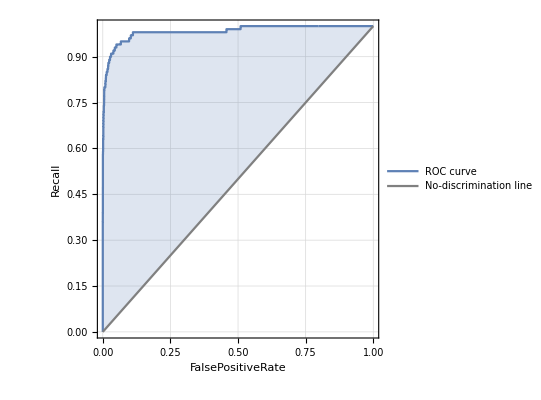
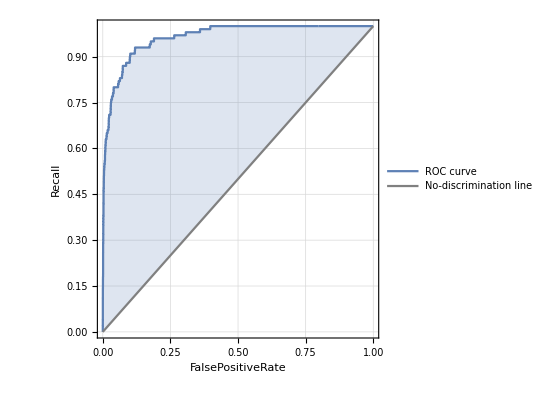
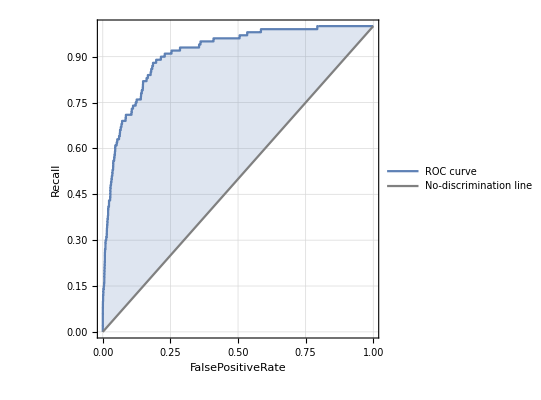
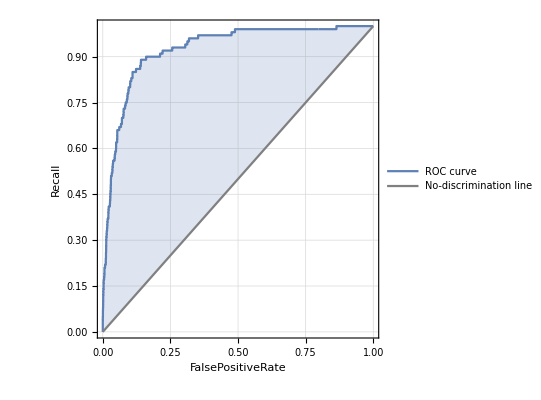
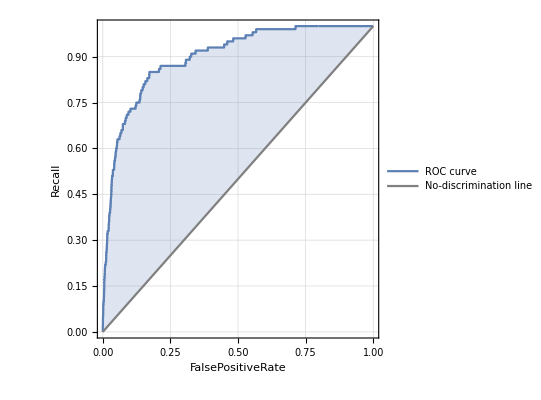
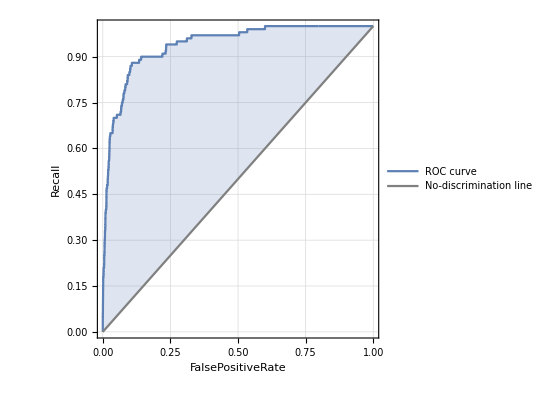
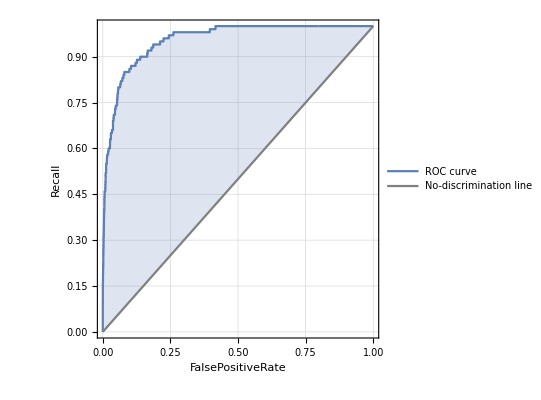
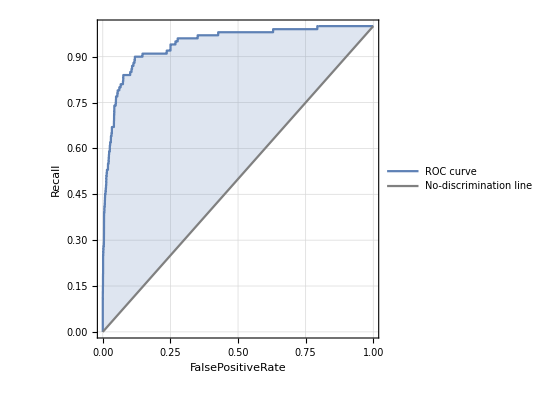
<|apple→-Graphics-,aquarium fish→-Graphics-,baby→-Graphics-,bear→-Graphics-,beaver→-Graphics-,bed→-Graphics-,bee→-Graphics-,beetle→-Graphics-,bicycle→-Graphics-,bottle→-Graphics-,bowl→-Graphics-,boy→-Graphics-,bridge→-Graphics-,bus→-Graphics-,butterfly→-Graphics-,camel→-Graphics-,can→-Graphics-,castle→-Graphics-,caterpillar→-Graphics-,cattle→-Graphics-,chair→-Graphics-,chimpanzee→-Graphics-,clock→-Graphics-,cloud→-Graphics-,cockroach→-Graphics-,computer keyboard→-Graphics-,couch→-Graphics-,crab→-Graphics-,crocodile→-Graphics-,cup→-Graphics-,dinosaur→-Graphics-,dolphin→-Graphics-,elephant→-Graphics-,flatfish→-Graphics-,forest→-Graphics-,fox→-Graphics-,girl→-Graphics-,hamster→-Graphics-,house→-Graphics-,kangaroo→-Graphics-,lamp→-Graphics-,lawn-mower→-Graphics-,leopard→-Graphics-,lion→-Graphics-,lizard→-Graphics-,lobster→-Graphics-,man→-Graphics-,maple tree→-Graphics-,motorcycle→-Graphics-,mountain→-Graphics-,mouse→-Graphics-,mushroom→-Graphics-,oak tree→-Graphics-,orange→-Graphics-,orchid→-Graphics-,otter→-Graphics-,palm tree→-Graphics-,pear→-Graphics-,pickup truck→-Graphics-,pine tree→-Graphics-,plain→-Graphics-,plate→-Graphics-,poppy→-Graphics-,porcupine→-Graphics-,possum→-Graphics-,rabbit→-Graphics-,raccoon→-Graphics-,ray→-Graphics-,road→-Graphics-,rocket→-Graphics-,rose→-Graphics-,sea→-Graphics-,seal→-Graphics-,shark→-Graphics-,shrew→-Graphics-,skunk→-Graphics-,skyscraper→-Graphics-,snail→-Graphics-,snake→-Graphics-,spider→-Graphics-,squirrel→-Graphics-,streetcar→-Graphics-,sunflower→-Graphics-,sweet pepper→-Graphics-,table→-Graphics-,tank→-Graphics-,telephone→-Graphics-,television→-Graphics-,tiger→-Graphics-,tractor→-Graphics-,train→-Graphics-,trout→-Graphics-,tulip→-Graphics-,turtle→-Graphics-,wardrobe→-Graphics-,whale→-Graphics-,willow tree→-Graphics-,wolf→-Graphics-,woman→-Graphics-,worm→-Graphics-|>

```mathematica
cm/@{"ROCCurve"}//TableForm
```

```mathematica
ClassifierMeasurements[c,testData,"Precision"]
```

<|apple→0.634783,aquarium fish→0.45082,baby→0.21875,bear→0.285714,beaver→0.202381,bed→0.27193,bee→0.366071,beetle→0.424658,bicycle→0.557143,bottle→0.535354,bowl→0.225806,boy→0.264706,bridge→0.493151,bus→0.368421,butterfly→0.5,camel→0.285714,can→0.434783,castle→0.617284,caterpillar→0.450704,cattle→0.319444,chair→0.589744,chimpanzee→0.392857,clock→0.490909,cloud→0.503704,cockroach→0.641509,computer keyboard→0.464286,couch→0.338028,crab→0.384615,crocodile→0.175299,cup→0.547826,dinosaur→0.714286,dolphin→0.510204,elephant→0.325758,flatfish→0.21547,forest→0.368932,fox→0.190476,girl→0.266667,hamster→0.197183,house→0.323232,kangaroo→0.157676,lamp→0.371429,lawn-mower→0.558559,leopard→0.391304,lion→0.292208,lizard→0.207317,lobster→0.257143,man→0.255814,maple tree→0.392857,motorcycle→0.74359,mountain→0.55,mouse→0.371429,mushroom→0.35443,oak tree→0.555556,orange→0.701493,orchid→0.576087,otter→0.135593,palm tree→0.466667,pear→0.387387,pickup truck→0.512195,pine tree→0.393939,plain→0.8,plate→0.555556,poppy→0.34375,porcupine→0.407407,possum→0.127753,rabbit→0.323529,raccoon→0.278351,ray→0.333333,road→0.683168,rocket→0.484848,rose→0.377358,sea→0.558824,seal→0.188679,shark→0.303704,shrew→0.2,skunk→0.725,skyscraper→0.605263,snail→0.271186,snake→0.247423,spider→0.409091,squirrel→0.191489,streetcar→0.308824,sunflower→0.735632,sweet pepper→0.449275,table→0.463415,tank→0.704918,telephone→0.625,television→0.384,tiger→0.258065,tractor→0.392157,train→0.248619,trout→0.429825,tulip→0.236364,turtle→0.466667,wardrobe→0.7,whale→0.364238,willow tree→0.336207,wolf→0.311321,woman→0.151316,worm→0.260274|>

```mathematica
ClassifierMeasurements[c,testData,"Recall"]
```

<|apple→0.73,aquarium fish→0.55,baby→0.21,bear→0.08,beaver→0.17,bed→0.31,bee→0.41,beetle→0.31,bicycle→0.39,bottle→0.53,bowl→0.28,boy→0.18,bridge→0.36,bus→0.28,butterfly→0.27,camel→0.32,can→0.4,castle→0.5,caterpillar→0.32,cattle→0.23,chair→0.69,chimpanzee→0.55,clock→0.27,cloud→0.68,cockroach→0.68,computer keyboard→0.39,couch→0.24,crab→0.25,crocodile→0.44,cup→0.63,dinosaur→0.25,dolphin→0.25,elephant→0.43,flatfish→0.39,forest→0.38,fox→0.32,girl→0.12,hamster→0.42,house→0.32,kangaroo→0.38,lamp→0.39,lawn-mower→0.62,leopard→0.27,lion→0.45,lizard→0.17,lobster→0.18,man→0.22,maple tree→0.55,motorcycle→0.58,mountain→0.44,mouse→0.13,mushroom→0.28,oak tree→0.55,orange→0.47,orchid→0.53,otter→0.08,palm tree→0.49,pear→0.43,pickup truck→0.42,pine tree→0.26,plain→0.68,plate→0.4,poppy→0.55,porcupine→0.33,possum→0.29,rabbit→0.11,raccoon→0.27,ray→0.45,road→0.69,rocket→0.64,rose→0.2,sea→0.76,seal→0.1,shark→0.41,shrew→0.27,skunk→0.58,skyscraper→0.69,snail→0.16,snake→0.24,spider→0.36,squirrel→0.09,streetcar→0.42,sunflower→0.64,sweet pepper→0.31,table→0.19,tank→0.43,telephone→0.3,television→0.48,tiger→0.24,tractor→0.4,train→0.45,trout→0.49,tulip→0.26,turtle→0.14,wardrobe→0.7,whale→0.55,willow tree→0.39,wolf→0.33,woman→0.23,worm→0.38|>

```mathematica
ClassifierMeasurements[c,testData,"Accuracy"]
```

0.3802